```mathematica
V[ϕ[t]]==-f2^(3+3 w) P0 a[t]^(-3 (1+w))+(6 f2^2 K ϕ[t])/a[t]^2+6 f2^(6 w) a[t]^(-6 w) H[t] (H[t] ϕ[t]+ϕ'[t])

H'[t]==(-2+3 w) H[t]^2+1/6 f2^(-6 w) a[t]^(-2+6 w) (-6 f2^2 K+a[t]^2 V'[ϕ[t]])

1/2 f2^(3-3 w) P0 (1+w) a[t]^(-3+3 w)-4 f2^(2-6 w) K a[t]^(-2+6 w) ϕ[t]+1/3 f2^(-6 w) a[t]^(6 w) ϕ[t] V'[ϕ[t]]-H[t] (4 H[t] ϕ[t]+(1+3 w) ϕ'[t])+ϕ''[t]==0


Solve[%,ϕ''[t]];

FullSimplify[%]
```

V[ϕ[t]]==-f2^(3+3 w) P0 a[t]^(-3 (1+w))+(6 f2^2 K ϕ[t])/a[t]^2+6 f2^(6 w) a[t]^(-6 w) H[t] (H[t] ϕ[t]+ϕ'[t])

H'[t]==(-2+3 w) H[t]^2+1/6 f2^(-6 w) a[t]^(-2+6 w) (-6 f2^2 K+a[t]^2 V'[ϕ[t]])

1/2 f2^(3-3 w) P0 (1+w) a[t]^(-3+3 w)-4 f2^(2-6 w) K a[t]^(-2+6 w) ϕ[t]+1/3 f2^(-6 w) a[t]^(6 w) ϕ[t] V'[ϕ[t]]-H[t] (4 H[t] ϕ[t]+(1+3 w) ϕ'[t])+ϕ''[t]==0

{{ϕ''[t]→-1/2 f2^(3-3 w) P0 (1+w) a[t]^(-3+3 w)-1/3 f2^(-6 w) a[t]^(-2+6 w) ϕ[t] (-12 f2^2 K+a[t]^2 V'[ϕ[t]])+H[t] (4 H[t] ϕ[t]+(1+3 w) ϕ'[t])}}

```mathematica
Ne==Log[a[t]]
```

Ne==Log[a[t]]

```mathematica
ϕ'[t]->ϕ'[Ne[t]]*H[Ne[t]]

D[%,t]

ReplaceAll[%,Ne'[t]->H[Ne]]

FullSimplify[%]
```

ϕ'[t]→H[Ne[t]] ϕ'[Ne[t]]

ϕ''[t]→H'[Ne[t]] Ne'[t] ϕ'[Ne[t]]+H[Ne[t]] Ne'[t] ϕ''[Ne[t]]

ϕ''[t]→H[Ne] H'[Ne[t]] ϕ'[Ne[t]]+H[Ne] H[Ne[t]] ϕ''[Ne[t]]

ϕ''[t]→H[Ne] (H'[Ne[t]] ϕ'[Ne[t]]+H[Ne[t]] ϕ''[Ne[t]])

```mathematica
V[ϕ[t]]==-f2^(3+3 w) P0 a[t]^(-3 (1+w))+(6 f2^2 K ϕ[t])/a[t]^2+6 f2^(6 w) a[t]^(-6 w) H[t] (H[t] ϕ[t]+ϕ'[t])

ReplaceAll[%,ϕ'[t]->H[Ne] ϕ'[Ne]]

ReplaceAll[%,H[t]->H[Ne]]

ReplaceAll[%,ϕ[t]->ϕ[Ne]]

ReplaceAll[%,a[t]->Exp[Ne]]

PowerExpand[%]

Expand[%]

ReplaceAll[%,H[Ne]^2->X]

Solve[%,X];

FullSimplify[%]

H[Ne]^2 ->FullSimplify[ⅇ^(3 Ne (-1+w)) f2^(-6 w) (f2^(3+3 w) P0)/(6 (ϕ[Ne]+ϕ'[Ne]))]+FullSimplify[(ⅇ^(3 Ne (-1+w)) f2^(-6 w) *ⅇ^(2 Ne)*(ⅇ^(Ne+3 Ne w) ))/(6 (ϕ[Ne]+ϕ'[Ne]))]*( V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]/ⅇ^(2 Ne))
```

V[ϕ[t]]==-f2^(3+3 w) P0 a[t]^(-3 (1+w))+(6 f2^2 K ϕ[t])/a[t]^2+6 f2^(6 w) a[t]^(-6 w) H[t] (H[t] ϕ[t]+ϕ'[t])

V[ϕ[t]]==-f2^(3+3 w) P0 a[t]^(-3 (1+w))+(6 f2^2 K ϕ[t])/a[t]^2+6 f2^(6 w) a[t]^(-6 w) H[t] (H[t] ϕ[t]+H[Ne] ϕ'[Ne])

V[ϕ[t]]==-f2^(3+3 w) P0 a[t]^(-3 (1+w))+(6 f2^2 K ϕ[t])/a[t]^2+6 f2^(6 w) a[t]^(-6 w) H[Ne] (H[Ne] ϕ[t]+H[Ne] ϕ'[Ne])

V[ϕ[Ne]]==-f2^(3+3 w) P0 a[t]^(-3 (1+w))+(6 f2^2 K ϕ[Ne])/a[t]^2+6 f2^(6 w) a[t]^(-6 w) H[Ne] (H[Ne] ϕ[Ne]+H[Ne] ϕ'[Ne])

V[ϕ[Ne]]==-(ⅇ^Ne)^(-3 (1+w)) f2^(3+3 w) P0+6 ⅇ^(-2 Ne) f2^2 K ϕ[Ne]+6 (ⅇ^Ne)^(-6 w) f2^(6 w) H[Ne] (H[Ne] ϕ[Ne]+H[Ne] ϕ'[Ne])

V[ϕ[Ne]]==-ⅇ^(-3 Ne (1+w)) f2^(3+3 w) P0+6 ⅇ^(-2 Ne) f2^2 K ϕ[Ne]+6 ⅇ^(-6 Ne w) f2^(6 w) H[Ne] (H[Ne] ϕ[Ne]+H[Ne] ϕ'[Ne])

V[ϕ[Ne]]==-ⅇ^(-3 Ne (1+w)) f2^(3+3 w) P0+6 ⅇ^(-2 Ne) f2^2 K ϕ[Ne]+6 ⅇ^(-6 Ne w) f2^(6 w) H[Ne]^2 ϕ[Ne]+6 ⅇ^(-6 Ne w) f2^(6 w) H[Ne]^2 ϕ'[Ne]

V[ϕ[Ne]]==-ⅇ^(-3 Ne (1+w)) f2^(3+3 w) P0+6 ⅇ^(-2 Ne) f2^2 K ϕ[Ne]+6 ⅇ^(-6 Ne w) f2^(6 w) X ϕ[Ne]+6 ⅇ^(-6 Ne w) f2^(6 w) X ϕ'[Ne]

{{X→(ⅇ^(3 Ne (-1+w)) f2^(-6 w) (f2^(3+3 w) P0+ⅇ^(Ne+3 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne])))/(6 (ϕ[Ne]+ϕ'[Ne]))}}

H[Ne]^2→(ⅇ^(3 Ne (-1+w)) f2^(3-3 w) P0)/(6 (ϕ[Ne]+ϕ'[Ne]))+(ⅇ^(6 Ne w) f2^(-6 w) (V[ϕ[Ne]]-6 ⅇ^(-2 Ne) f2^2 K ϕ[Ne]))/(6 (ϕ[Ne]+ϕ'[Ne]))

```mathematica
H'[t]==(-2+3 w) H[t]^2+1/6 f2^(-6 w) a[t]^(-2+6 w) (-6 f2^2 K+a[t]^2 V'[ϕ[t]])

ReplaceAll[%,H'[t]->H[Ne]*H'[Ne]]

ReplaceAll[%,H[t]->H[Ne]]

ReplaceAll[%,ϕ[t]->ϕ[Ne]]

ReplaceAll[%,a[t]->Exp[Ne]]

PowerExpand[%]

Solve[%,H'[Ne]];

FullSimplify[%]
```

H'[t]==(-2+3 w) H[t]^2+1/6 f2^(-6 w) a[t]^(-2+6 w) (-6 f2^2 K+a[t]^2 V'[ϕ[t]])

H[Ne] H'[Ne]==(-2+3 w) H[t]^2+1/6 f2^(-6 w) a[t]^(-2+6 w) (-6 f2^2 K+a[t]^2 V'[ϕ[t]])

H[Ne] H'[Ne]==(-2+3 w) H[Ne]^2+1/6 f2^(-6 w) a[t]^(-2+6 w) (-6 f2^2 K+a[t]^2 V'[ϕ[t]])

H[Ne] H'[Ne]==(-2+3 w) H[Ne]^2+1/6 f2^(-6 w) a[t]^(-2+6 w) (-6 f2^2 K+a[t]^2 V'[ϕ[Ne]])

H[Ne] H'[Ne]==(-2+3 w) H[Ne]^2+1/6 (ⅇ^Ne)^(-2+6 w) f2^(-6 w) (-6 f2^2 K+ⅇ^(2 Ne) V'[ϕ[Ne]])

H[Ne] H'[Ne]==(-2+3 w) H[Ne]^2+1/6 ⅇ^(Ne (-2+6 w)) f2^(-6 w) (-6 f2^2 K+ⅇ^(2 Ne) V'[ϕ[Ne]])

{{H'[Ne]→(-2+3 w) H[Ne]+(f2^(-6 w) (-6 ⅇ^(Ne (-2+6 w)) f2^2 K+ⅇ^(6 Ne w) V'[ϕ[Ne]]))/(6 H[Ne])}}

```mathematica
ϵ[Ne]->-H'[Ne]/H[Ne]

ReplaceAll[%,H'[Ne]->(-2+3 w) H[Ne]+(f2^(-6 w) (-6 ⅇ^(Ne (-2+6 w)) f2^2 K+ⅇ^(6 Ne w) V'[ϕ[Ne]]))/(6 H[Ne])]

ReplaceAll[%,H[Ne]->Sqrt[(ⅇ^(3 Ne (-1+w)) f2^(3-3 w) P0)/(6 (ϕ[Ne]+ϕ'[Ne]))+(ⅇ^(6 Ne w) f2^(-6 w) (V[ϕ[Ne]]-6 ⅇ^(-2 Ne) f2^2 K ϕ[Ne]))/(6 (ϕ[Ne]+ϕ'[Ne]))]]

FullSimplify[%]

Expand[%]
```

ϵ[Ne]→-H'[Ne]/H[Ne]

ϵ[Ne]→-((-2+3 w) H[Ne]+(f2^(-6 w) (-6 ⅇ^(Ne (-2+6 w)) f2^2 K+ⅇ^(6 Ne w) V'[ϕ[Ne]]))/(6 H[Ne]))/H[Ne]

ϵ[Ne]→-((f2^(-6 w) (-6 ⅇ^(Ne (-2+6 w)) f2^2 K+ⅇ^(6 Ne w) V'[ϕ[Ne]]))/(6 √((ⅇ^(3 Ne (-1+w)) f2^(3-3 w) P0)/(6 (ϕ[Ne]+ϕ'[Ne]))+(ⅇ^(6 Ne w) f2^(-6 w) (V[ϕ[Ne]]-6 ⅇ^(-2 Ne) f2^2 K ϕ[Ne]))/(6 (ϕ[Ne]+ϕ'[Ne]))))+(-2+3 w) √((ⅇ^(3 Ne (-1+w)) f2^(3-3 w) P0)/(6 (ϕ[Ne]+ϕ'[Ne]))+(ⅇ^(6 Ne w) f2^(-6 w) (V[ϕ[Ne]]-6 ⅇ^(-2 Ne) f2^2 K ϕ[Ne]))/(6 (ϕ[Ne]+ϕ'[Ne]))))/(√((ⅇ^(3 Ne (-1+w)) f2^(3-3 w) P0)/(6 (ϕ[Ne]+ϕ'[Ne]))+(ⅇ^(6 Ne w) f2^(-6 w) (V[ϕ[Ne]]-6 ⅇ^(-2 Ne) f2^2 K ϕ[Ne]))/(6 (ϕ[Ne]+ϕ'[Ne]))))

ϵ[Ne]→-((ⅇ^(Ne (-1+3 w)) (f2^(3+3 w) P0 (-2+3 w)+ⅇ^(3 Ne (1+w)) (-2+3 w) V[ϕ[Ne]]+ⅇ^(Ne+3 Ne w) (ⅇ^(2 Ne) V'[ϕ[Ne]] (ϕ[Ne]+ϕ'[Ne])-6 f2^2 K ((-1+3 w) ϕ[Ne]+ϕ'[Ne]))))/(ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne])))

ϵ[Ne]→(2 ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0)/(ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))-(3 ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0 w)/(ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))+(2 ⅇ^(3 Ne (1+w)+Ne (-1+3 w)) V[ϕ[Ne]])/(ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))-(3 ⅇ^(3 Ne (1+w)+Ne (-1+3 w)) w V[ϕ[Ne]])/(ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))-(6 ⅇ^(Ne+3 Ne w+Ne (-1+3 w)) f2^2 K ϕ[Ne])/(ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))+(18 ⅇ^(Ne+3 Ne w+Ne (-1+3 w)) f2^2 K w ϕ[Ne])/(ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))-(ⅇ^(3 Ne+3 Ne w+Ne (-1+3 w)) ϕ[Ne] V'[ϕ[Ne]])/(ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))+(6 ⅇ^(Ne+3 Ne w+Ne (-1+3 w)) f2^2 K ϕ'[Ne])/(ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))-(ⅇ^(3 Ne+3 Ne w+Ne (-1+3 w)) V'[ϕ[Ne]] ϕ'[Ne])/(ⅇ^(Ne (-1+3 w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))

```mathematica
ϕ''[t]==-1/2 f2^(3-3 w) P0 (1+w) a[t]^(-3+3 w)-1/3 f2^(-6 w) a[t]^(-2+6 w) ϕ[t] (-12 f2^2 K+a[t]^2 V'[ϕ[t]])+H[t] (4 H[t] ϕ[t]+(1+3 w) ϕ'[t])

ReplaceAll[%,ϕ''[t]->H[Ne] (H'[Ne] ϕ'[Ne]+H[Ne] ϕ''[Ne])]

ReplaceAll[%,ϕ'[t]->H[Ne] ϕ'[Ne]]

ReplaceAll[%,H[t]->H[Ne]]

ReplaceAll[%,ϕ[t]->ϕ[Ne]]

ReplaceAll[%,a[t]->Exp[Ne]]

ReplaceAll[%,H'[Ne]->(-2+3 w) H[Ne]+(f2^(-6 w) (-6 ⅇ^(Ne (-2+6 w)) f2^2 K+ⅇ^(6 Ne w) V'[ϕ[Ne]]))/(6 H[Ne])];

PowerExpand[%]

Solve[%,ϕ''[Ne]];

FullSimplify[%]

ReplaceAll[%,H[Ne]->Sqrt[(ⅇ^(3 Ne (-1+w)) f2^(-6 w) (f2^(3+3 w) P0+ⅇ^(Ne+3 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne])))/(6 (ϕ[Ne]+ϕ'[Ne]))]];

FullSimplify[%];

PowerExpand[%]

FullSimplify[%]

Expand[%];

Collect[%,{ϕ'[Ne]}];

FullSimplify[%]
```

ϕ''[t]==-1/2 f2^(3-3 w) P0 (1+w) a[t]^(-3+3 w)-1/3 f2^(-6 w) a[t]^(-2+6 w) ϕ[t] (-12 f2^2 K+a[t]^2 V'[ϕ[t]])+H[t] (4 H[t] ϕ[t]+(1+3 w) ϕ'[t])

H[Ne] (H'[Ne] ϕ'[Ne]+H[Ne] ϕ''[Ne])==-1/2 f2^(3-3 w) P0 (1+w) a[t]^(-3+3 w)-1/3 f2^(-6 w) a[t]^(-2+6 w) ϕ[t] (-12 f2^2 K+a[t]^2 V'[ϕ[t]])+H[t] (4 H[t] ϕ[t]+(1+3 w) ϕ'[t])

H[Ne] (H'[Ne] ϕ'[Ne]+H[Ne] ϕ''[Ne])==-1/2 f2^(3-3 w) P0 (1+w) a[t]^(-3+3 w)-1/3 f2^(-6 w) a[t]^(-2+6 w) ϕ[t] (-12 f2^2 K+a[t]^2 V'[ϕ[t]])+H[t] (4 H[t] ϕ[t]+(1+3 w) H[Ne] ϕ'[Ne])

H[Ne] (H'[Ne] ϕ'[Ne]+H[Ne] ϕ''[Ne])==-1/2 f2^(3-3 w) P0 (1+w) a[t]^(-3+3 w)-1/3 f2^(-6 w) a[t]^(-2+6 w) ϕ[t] (-12 f2^2 K+a[t]^2 V'[ϕ[t]])+H[Ne] (4 H[Ne] ϕ[t]+(1+3 w) H[Ne] ϕ'[Ne])

H[Ne] (H'[Ne] ϕ'[Ne]+H[Ne] ϕ''[Ne])==-1/2 f2^(3-3 w) P0 (1+w) a[t]^(-3+3 w)-1/3 f2^(-6 w) a[t]^(-2+6 w) ϕ[Ne] (-12 f2^2 K+a[t]^2 V'[ϕ[Ne]])+H[Ne] (4 H[Ne] ϕ[Ne]+(1+3 w) H[Ne] ϕ'[Ne])

H[Ne] (H'[Ne] ϕ'[Ne]+H[Ne] ϕ''[Ne])==-1/2 (ⅇ^Ne)^(-3+3 w) f2^(3-3 w) P0 (1+w)-1/3 (ⅇ^Ne)^(-2+6 w) f2^(-6 w) ϕ[Ne] (-12 f2^2 K+ⅇ^(2 Ne) V'[ϕ[Ne]])+H[Ne] (4 H[Ne] ϕ[Ne]+(1+3 w) H[Ne] ϕ'[Ne])

H[Ne] (((-2+3 w) H[Ne]+(f2^(-6 w) (-6 ⅇ^(Ne (-2+6 w)) f2^2 K+ⅇ^(6 Ne w) V'[ϕ[Ne]]))/(6 H[Ne])) ϕ'[Ne]+H[Ne] ϕ''[Ne])==-1/2 ⅇ^(Ne (-3+3 w)) f2^(3-3 w) P0 (1+w)-1/3 ⅇ^(Ne (-2+6 w)) f2^(-6 w) ϕ[Ne] (-12 f2^2 K+ⅇ^(2 Ne) V'[ϕ[Ne]])+H[Ne] (4 H[Ne] ϕ[Ne]+(1+3 w) H[Ne] ϕ'[Ne])

{{ϕ''[Ne]→4 ϕ[Ne]+3 ϕ'[Ne]-1/(6 H[Ne]^2)ⅇ^(3 Ne (-1+w)) f2^(-6 w) (3 f2^(3+3 w) P0 (1+w)+ⅇ^(Ne+3 Ne w) (ⅇ^(2 Ne) V'[ϕ[Ne]] (2 ϕ[Ne]+ϕ'[Ne])-6 f2^2 K (4 ϕ[Ne]+ϕ'[Ne])))}}

{{ϕ''[Ne]→4 ϕ[Ne]+3 ϕ'[Ne]-((ϕ[Ne]+ϕ'[Ne]) (3 f2^(3+3 w) P0 (1+w)+ⅇ^(Ne+3 Ne w) (ⅇ^(2 Ne) V'[ϕ[Ne]] (2 ϕ[Ne]+ϕ'[Ne])-6 f2^2 K (4 ϕ[Ne]+ϕ'[Ne]))))/(f2^(3+3 w) P0+ⅇ^(Ne+3 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))}}

{{ϕ''[Ne]→4 ϕ[Ne]+3 ϕ'[Ne]-((ϕ[Ne]+ϕ'[Ne]) (3 f2^(3+3 w) P0 (1+w)+ⅇ^(Ne+3 Ne w) (ⅇ^(2 Ne) V'[ϕ[Ne]] (2 ϕ[Ne]+ϕ'[Ne])-6 f2^2 K (4 ϕ[Ne]+ϕ'[Ne]))))/(f2^(3+3 w) P0+ⅇ^(Ne+3 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))}}

{{ϕ''[Ne]→(-2 ⅇ^(3 Ne (1+w)) ϕ[Ne]^2 V'[ϕ[Ne]]+ϕ[Ne] (-f2^(3+3 w) P0 (-1+3 w)+4 ⅇ^(3 Ne (1+w)) V[ϕ[Ne]]-3 ⅇ^(Ne+3 Ne w) (-4 f2^2 K+ⅇ^(2 Ne) V'[ϕ[Ne]]) ϕ'[Ne])+ϕ'[Ne] (-3 f2^(3+3 w) P0 w+ⅇ^(Ne+3 Ne w) (6 f2^2 K ϕ'[Ne]+ⅇ^(2 Ne) (3 V[ϕ[Ne]]-V'[ϕ[Ne]] ϕ'[Ne]))))/(f2^(3+3 w) P0+ⅇ^(Ne+3 Ne w) (ⅇ^(2 Ne) V[ϕ[Ne]]-6 f2^2 K ϕ[Ne]))}}

```mathematica
𝒰[ϕ[Ne]]==ϕ'[Ne]

𝒰'[ϕ[Ne]]*𝒰[ϕ[Ne]]==4 ϕ[Ne]-(2 ϕ[Ne]^2 V'[ϕ[Ne]])/V[ϕ[Ne]]+3 ϕ'[Ne]-(3 ϕ[Ne] V'[ϕ[Ne]] ϕ'[Ne])/V[ϕ[Ne]]-(V'[ϕ[Ne]] ϕ'[Ne]^2)/V[ϕ[Ne]]

ReplaceAll[%,ϕ'[Ne]->𝒰[ϕ[Ne]]]

Solve[%,𝒰'[ϕ[Ne]]]

FullSimplify[%]

Expand[%]
```

𝒰[ϕ[Ne]]==ϕ'[Ne]

𝒰[ϕ[Ne]] 𝒰'[ϕ[Ne]]==4 ϕ[Ne]-(2 ϕ[Ne]^2 V'[ϕ[Ne]])/V[ϕ[Ne]]+3 ϕ'[Ne]-(3 ϕ[Ne] V'[ϕ[Ne]] ϕ'[Ne])/V[ϕ[Ne]]-(V'[ϕ[Ne]] ϕ'[Ne]^2)/V[ϕ[Ne]]

𝒰[ϕ[Ne]] 𝒰'[ϕ[Ne]]==3 𝒰[ϕ[Ne]]+4 ϕ[Ne]-(𝒰[ϕ[Ne]]^2 V'[ϕ[Ne]])/V[ϕ[Ne]]-(3 𝒰[ϕ[Ne]] ϕ[Ne] V'[ϕ[Ne]])/V[ϕ[Ne]]-(2 ϕ[Ne]^2 V'[ϕ[Ne]])/V[ϕ[Ne]]

{{𝒰'[ϕ[Ne]]→1/(V[ϕ[Ne]] 𝒰[ϕ[Ne]])(3 V[ϕ[Ne]] 𝒰[ϕ[Ne]]+4 V[ϕ[Ne]] ϕ[Ne]-𝒰[ϕ[Ne]]^2 V'[ϕ[Ne]]-3 𝒰[ϕ[Ne]] ϕ[Ne] V'[ϕ[Ne]]-2 ϕ[Ne]^2 V'[ϕ[Ne]])}}

{{𝒰'[ϕ[Ne]]→(V[ϕ[Ne]] (3 𝒰[ϕ[Ne]]+4 ϕ[Ne])-(𝒰[ϕ[Ne]]+ϕ[Ne]) (𝒰[ϕ[Ne]]+2 ϕ[Ne]) V'[ϕ[Ne]])/(V[ϕ[Ne]] 𝒰[ϕ[Ne]])}}

{{𝒰'[ϕ[Ne]]→3+(4 ϕ[Ne])/𝒰[ϕ[Ne]]-(𝒰[ϕ[Ne]] V'[ϕ[Ne]])/V[ϕ[Ne]]-(3 ϕ[Ne] V'[ϕ[Ne]])/V[ϕ[Ne]]-(2 ϕ[Ne]^2 V'[ϕ[Ne]])/(V[ϕ[Ne]] 𝒰[ϕ[Ne]])}}

```mathematica
V[ϕ_]:=(ϕ-η)^2/(4*λ)
```

```mathematica
𝒰'[ϕ[Ne]]->3+(4 ϕ[Ne])/𝒰[ϕ[Ne]]-(𝒰[ϕ[Ne]] V'[ϕ[Ne]])/V[ϕ[Ne]]-(3 ϕ[Ne] V'[ϕ[Ne]])/V[ϕ[Ne]]-(2 ϕ[Ne]^2 V'[ϕ[Ne]])/(V[ϕ[Ne]] 𝒰[ϕ[Ne]])
```

𝒰'[ϕ[Ne]]→3+(4 ϕ[Ne])/𝒰[ϕ[Ne]]-(2 𝒰[ϕ[Ne]])/(-η+ϕ[Ne])-(6 ϕ[Ne])/(-η+ϕ[Ne])-(4 ϕ[Ne]^2)/(𝒰[ϕ[Ne]] (-η+ϕ[Ne]))

```mathematica
"ϕ[Ne]>>η"
```

ϕ[Ne]>>η

```mathematica
𝒰'[ϕ[Ne]]->3+(4 ϕ[Ne])/𝒰[ϕ[Ne]]-(2 𝒰[ϕ[Ne]])/(-η+ϕ[Ne])-(6 ϕ[Ne])/(-η+ϕ[Ne])-(4 ϕ[Ne]^2)/(𝒰[ϕ[Ne]] (-η+ϕ[Ne]))

ReplaceAll[%,η->0]
```

𝒰'[ϕ[Ne]]→3+(4 ϕ[Ne])/𝒰[ϕ[Ne]]-(2 𝒰[ϕ[Ne]])/(-η+ϕ[Ne])-(6 ϕ[Ne])/(-η+ϕ[Ne])-(4 ϕ[Ne]^2)/(𝒰[ϕ[Ne]] (-η+ϕ[Ne]))

𝒰'[ϕ[Ne]]→-3-(2 𝒰[ϕ[Ne]])/ϕ[Ne]

```mathematica
DSolve[𝒰'[ϕ[Ne]]==-3-(2 𝒰[ϕ[Ne]])/ϕ[Ne],𝒰[ϕ[Ne]],ϕ[Ne]]
```

{{𝒰[ϕ[Ne]]→C[1]/ϕ[Ne]^2-ϕ[Ne]}}

```mathematica
DSolve[ϕ'[Ne]==C1/ϕ[Ne]^2-ϕ[Ne],ϕ[Ne],Ne]
```

{{ϕ[Ne]→(C1+ⅇ^(-3 Ne+3 C[1]))^(1/3)},{ϕ[Ne]→-(-1)^(1/3) (C1+ⅇ^(-3 Ne+3 C[1]))^(1/3)},{ϕ[Ne]→(-1)^(2/3) (C1+ⅇ^(-3 Ne+3 C[1]))^(1/3)}}

```mathematica
ϕ[Ne]->(C1+ⅇ^(-3 Ne+3 C2))^(1/3)

D[%,Ne]
```

ϕ[Ne]→(C1+ⅇ^(3 C2-3 Ne))^(1/3)

ϕ'[Ne]→-ⅇ^(3 C2-3 Ne)/((C1+ⅇ^(3 C2-3 Ne))^(2/3))

```mathematica
V[ϕ_]:=(ϕ-η)^2/(4*λ)
```

```mathematica
1+q[Ne]==2-3 w-(ⅇ^(6 Ne w) ϕ[Ne] V'[ϕ[Ne]])/(ⅇ^(3 Ne (-1+w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) V[ϕ[Ne]])-(ⅇ^(6 Ne w) V'[ϕ[Ne]] ϕ'[Ne])/(ⅇ^(3 Ne (-1+w)) f2^(3+3 w) P0+ⅇ^(6 Ne w) V[ϕ[Ne]])

Solve[%,q[Ne]];

ReplaceAll[%,P0->0];

ReplaceAll[%,ϕ'[Ne]->-ⅇ^(3 C2-3 Ne)/((C1+ⅇ^(3 C2-3 Ne))^(2/3))];

ReplaceAll[%,ϕ[Ne]->(C1+ⅇ^(3 C2-3 Ne))^(1/3)];

ReplaceAll[%,η->0];

FullSimplify[%]
```

1+q[Ne]==2-3 w-(ⅇ^(6 Ne w) ϕ[Ne] (-η+ϕ[Ne]))/(2 λ (ⅇ^(3 Ne (-1+w)) f2^(3+3 w) P0+(ⅇ^(6 Ne w) (-η+ϕ[Ne])^2)/(4 λ)))-(ⅇ^(6 Ne w) (-η+ϕ[Ne]) ϕ'[Ne])/(2 λ (ⅇ^(3 Ne (-1+w)) f2^(3+3 w) P0+(ⅇ^(6 Ne w) (-η+ϕ[Ne])^2)/(4 λ)))

{{q[Ne]→-1+2/(1+C1 ⅇ^(-3 C2+3 Ne))-3 w}}

```mathematica
q[Ne]->1-3 w+FullSimplify[(2 C1 ⅇ^(3 Ne))/(-ⅇ^(3 C2)-C1 ⅇ^(3 Ne)+ⅇ^(3 Ne) η^3)+(2 C1 ⅇ^(6 Ne) (C1+ⅇ^(3 C2-3 Ne))^(2/3) η)/((ⅇ^(3 C2)+C1 ⅇ^(3 Ne)) (-ⅇ^(3 C2)-C1 ⅇ^(3 Ne)+ⅇ^(3 Ne) η^3))+(2 C1 ⅇ^(6 Ne) (C1+ⅇ^(3 C2-3 Ne))^(1/3) η^2)/((ⅇ^(3 C2)+C1 ⅇ^(3 Ne)) (-ⅇ^(3 C2)-C1 ⅇ^(3 Ne)+ⅇ^(3 Ne) η^3))]
```

q[Ne]→1-3 w-(2 C1 ⅇ^(3 Ne))/(ⅇ^(3 C2)+ⅇ^(3 Ne) (C1-(C1+ⅇ^(3 C2-3 Ne))^(2/3) η))

100

20

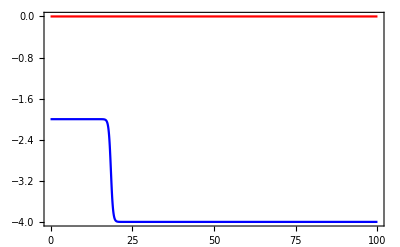

```mathematica
C1=100

C2=20
q[Ne_,w_]:=-1-3 w+2/(1+C1 ⅇ^(-3 C2+3 Ne))

Plot[{q[Ne,1],0},{Ne,0,100},PlotRange->Full,PlotRange->Automatic,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
"φ[Ne]<<η"
```

φ[Ne]<<η

```mathematica
ϕ[Ne]==η+φ[ϕ[Ne]]

Solve[%,φ[ϕ[Ne]]]

D[%,ϕ[Ne]]
```

ϕ[Ne]==η+φ[ϕ[Ne]]

{{φ[ϕ[Ne]]→-η+ϕ[Ne]}}

{{φ'[ϕ[Ne]]→1}}

```mathematica
φ[Ne]->-η+ϕ[Ne]

D[%,Ne]
```

φ[Ne]→-η+ϕ[Ne]

φ'[Ne]→ϕ'[Ne]

```mathematica
𝒰'[ϕ[Ne]]->3+(4 ϕ[Ne])/𝒰[ϕ[Ne]]-(2 𝒰[ϕ[Ne]])/(-η+ϕ[Ne])-(6 ϕ[Ne])/(-η+ϕ[Ne])-(4 ϕ[Ne]^2)/(𝒰[ϕ[Ne]] (-η+ϕ[Ne]))
```

𝒰'[ϕ[Ne]]→3+(4 ϕ[Ne])/𝒰[ϕ[Ne]]-(2 𝒰[ϕ[Ne]])/(-η+ϕ[Ne])-(6 ϕ[Ne])/(-η+ϕ[Ne])-(4 ϕ[Ne]^2)/(𝒰[ϕ[Ne]] (-η+ϕ[Ne]))

```mathematica
𝒰'[φ[Ne]]==-(6 η)/φ[Ne]-(4 η^2)/(𝒰[φ[Ne]] φ[Ne])-(2 𝒰[φ[Ne]])/φ[Ne]

𝒰'[φ[Ne]]==-(4 η^2)/(𝒰[φ[Ne]] φ[Ne])+FullSimplify[-(2 𝒰[φ[Ne]])/φ[Ne]-(6 η)/φ[Ne]]
```

𝒰'[φ[Ne]]==-(6 η)/φ[Ne]-(4 η^2)/(𝒰[φ[Ne]] φ[Ne])-(2 𝒰[φ[Ne]])/φ[Ne]

𝒰'[φ[Ne]]==-(4 η^2)/(𝒰[φ[Ne]] φ[Ne])-(2 (3 η+𝒰[φ[Ne]]))/φ[Ne]

```mathematica
"𝒰[φ[Ne]]>>η"
```

𝒰[φ[Ne]]>>η

```mathematica
𝒰'[φ[Ne]]==-(6 η)/φ[Ne]+FullSimplify[-(4 η^2)/(𝒰[φ[Ne]]*φ[Ne])-(2 𝒰[φ[Ne]])/φ[Ne]]
```

𝒰'[φ[Ne]]==-(6 η)/φ[Ne]-(2 (2 η^2+𝒰[φ[Ne]]^2))/(𝒰[φ[Ne]] φ[Ne])

```mathematica
𝒰'[φ[Ne]]==FullSimplify[-(6 η)/φ[Ne]-(2 (𝒰[φ[Ne]]^2))/(𝒰[φ[Ne]] φ[Ne])]
```

𝒰'[φ[Ne]]==-(2 (3 η+𝒰[φ[Ne]]))/φ[Ne]

```mathematica
𝒰'[φ[Ne]]==-(2 (𝒰[φ[Ne]]))/φ[Ne]
```

𝒰'[φ[Ne]]==-(2 𝒰[φ[Ne]])/φ[Ne]

```mathematica
DSolve[𝒰'[φ[Ne]]==-(2 𝒰[φ[Ne]])/φ[Ne],𝒰[φ[Ne]],φ[Ne]]

FullSimplify[%]
```

{{𝒰[φ[Ne]]→C[1]/φ[Ne]^2}}

{{𝒰[φ[Ne]]→C[1]/φ[Ne]^2}}

```mathematica
DSolve[φ'[Ne]==C1/(3*φ[Ne]^2),φ[Ne],Ne]
```

{{φ[Ne]→(C1 Ne+3 C[1])^(1/3)},{φ[Ne]→-(-1)^(1/3) (C1 Ne+3 C[1])^(1/3)},{φ[Ne]→(-1)^(2/3) (C1 Ne+3 C[1])^(1/3)}}

```mathematica
3*Integrate[φ^2,φ]==C1*Ne+C2

φ[Ne]==((C2+C1*Ne))^(1/3)

D[%,Ne]
```

φ^3==C2+C1 Ne

φ[Ne]==(C2+C1 Ne)^(1/3)

φ'[Ne]==C1/(3 (C2+C1 Ne)^(2/3))

```mathematica
(C2+C1 Ne)^(1/3)<η

 Ne<(η^3-C2)/C1

Expand[%]
```

(C2+C1 Ne)^(1/3)<η

Ne<(-C2+η^3)/C1

Ne<-C2/C1+η^3/C1

```mathematica
C1/(3 (C2+C1 Ne)^(2/3))>η

(C1/η)^(3/2)/(3 √3)>C2+C1 Ne

((C1/(3*η))^(3/2)-C2)/C1> Ne

Expand[%]
```

C1/(3 (C2+C1 Ne)^(2/3))>η

(C1/η)^(3/2)/(3 √3)>C2+C1 Ne

(-C2+(C1/η)^(3/2)/(3 √3))/C1>Ne

-C2/C1+(√(C1/η))/(3 √3 η)>Ne

```mathematica
Ne<-C2/C1+η^3/C1

Ne<-C2/C1+(√(C1/η))/(3 √3 η)
```

```mathematica
Reduce[Ne<-C2/C1+η^3/C1&&Ne<-C2/C1+(√(C1/η))/(3 √3 η)&&C1>0&&η>0]
```

C2∈ℝ&&η>0&&((0<C1≤3 η^3&&Ne<-C2/C1+(√(C1/η^3))/(3 √3))||(C1>3 η^3&&Ne<(-C2+η^3)/C1))

```mathematica
Reduce[-C2/C1+η^3/C1<-C2/C1+(√(C1/η))/(3 √3 η)&&C1>0&&η>0]
```

C2∈ℝ&&η>0&&C1>3 η^3

```mathematica
Reduce[-C2/C1+η^3/C1>-C2/C1+(√(C1/η))/(3 √3 η)&&C1>0&&η>0]
```

C2∈ℝ&&η>0&&0<C1<3 η^3

```mathematica
V[ϕ_]:=(ϕ-η)^2/(4*λ)
```

```mathematica
H[Ne]->(ⅇ^(3 Ne w) f2^(-3 w) √V[ϕ[Ne]])/(√6 √(ϕ[Ne]+ϕ'[Ne]))

PowerExpand[%]

ReplaceAll[%,ϕ'[Ne]->φ'[Ne]]

ReplaceAll[%,ϕ[Ne]->η+φ[Ne]]

FullSimplify[%]

"φ[Ne]<<η<<𝒰[φ[Ne]]"

"𝒰[φ[Ne]]>>η"

"𝒰[φ[Ne]]>>φ[Ne]"
```

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) √((-η+ϕ[Ne])^2/λ))/(2 √6 √(ϕ[Ne]+ϕ'[Ne]))

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) (-η+ϕ[Ne]))/(2 √6 √λ √(ϕ[Ne]+ϕ'[Ne]))

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) (-η+ϕ[Ne]))/(2 √6 √λ √(ϕ[Ne]+φ'[Ne]))

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) φ[Ne])/(2 √6 √λ √(η+φ[Ne]+φ'[Ne]))

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) φ[Ne])/(2 √6 √λ √(η+φ[Ne]+φ'[Ne]))

φ[Ne]<<η<<𝒰[φ[Ne]]

𝒰[φ[Ne]]>>η

𝒰[φ[Ne]]>>φ[Ne]

```mathematica
H[Ne]->(ⅇ^(3 Ne w) f2^(-3 w) φ[Ne])/(2 √6 √λ √φ'[Ne])

ReplaceAll[%,φ'[Ne]->C1/(3 (C2+C1 Ne)^(2/3))]

ReplaceAll[%,φ[Ne]->(C2+C1 Ne)^(1/3)]

PowerExpand[%]

FullSimplify[%]

PowerExpand[%]

FullSimplify[%]
```

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) φ[Ne])/(2 √6 √λ √φ'[Ne])

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) φ[Ne])/(2 √2 √(C1/(C2+C1 Ne)^(2/3)) √λ)

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) (C2+C1 Ne)^(1/3))/(2 √2 √(C1/(C2+C1 Ne)^(2/3)) √λ)

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) (C2+C1 Ne)^(2/3))/(2 √2 √C1 √λ)

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) (C2+C1 Ne)^(2/3))/(2 √2 √C1 √λ)

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) (C2+C1 Ne)^(2/3))/(2 √2 √C1 √λ)

«1 more identical outputs»

```mathematica
H[Ne]->(ⅇ^(3 Ne w) f2^(-3 w) (C2+C1 Ne)^(2/3))/(2 √2 √C1 √λ)

D[%,Ne]

FullSimplify[%]
```

H[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) (C2+C1 Ne)^(2/3))/(2 √2 √C1 √λ)

H'[Ne]→(√C1 ⅇ^(3 Ne w) f2^(-3 w))/(3 √2 (C2+C1 Ne)^(1/3) √λ)+(3 ⅇ^(3 Ne w) f2^(-3 w) (C2+C1 Ne)^(2/3) w)/(2 √2 √C1 √λ)

H'[Ne]→(ⅇ^(3 Ne w) f2^(-3 w) (2 C1+9 (C2+C1 Ne) w))/(6 √2 √C1 (C2+C1 Ne)^(1/3) √λ)

```mathematica
ϵ[Ne]==-H'[Ne]/H[Ne]

ReplaceAll[%,H'[Ne]->(ⅇ^(3 Ne w) f2^(-3 w) (2 C1+9 (C2+C1 Ne) w))/(6 √2 √C1 (C2+C1 Ne)^(1/3) √λ)]

ReplaceAll[%,H[Ne]->(ⅇ^(3 Ne w) f2^(-3 w) (C2+C1 Ne)^(2/3))/(2 √2 √C1 √λ)]

Apart[%,w]
```

ϵ[Ne]==-H'[Ne]/H[Ne]

ϵ[Ne]==-(ⅇ^(3 Ne w) f2^(-3 w) (2 C1+9 (C2+C1 Ne) w))/(6 √2 √C1 (C2+C1 Ne)^(1/3) √λ H[Ne])

ϵ[Ne]==-(2 C1+9 (C2+C1 Ne) w)/(3 (C2+C1 Ne))

ϵ[Ne]==-(2 C1)/(3 (C2+C1 Ne))-3 w

```mathematica
-(2 C1)/(3 (C2+C1 Ne))-3 w<1
```

-(2 C1)/(3 (C2+C1 Ne))-3 w<1

```mathematica
-(2 C1)/(3 (C2+C1 Ne))<1+3 w

Ne<-C2/C1+η^3/C1
```

-(2 C1)/(3 (C2+C1 Ne))<1+3 w

Ne<-C2/C1+η^3/C1

```mathematica
Reduce[-(2 C1)/(3 (C2+C1 Ne))>1+3 w&&((0<C1≤3 η^3&&Ne<-C2/C1+(√(C1/η^3))/(3 √3))||(C1>3 η^3&&Ne<(-C2+η^3)/C1))&& η>0&&0≤ w≤
1&&C1>0, Ne]
```

C2∈ℝ&&η>0&&C1>0&&0≤w≤1&&(-2 C1-3 C2-9 C2 w)/(3 C1+9 C1 w)<Ne<-C2/C1

```mathematica
(-2 C1-3 C2-9 C2 w)/(3 C1+9 C1 w)<Ne<-C2/C1

FullSimplify[%]
```

(-2 C1-3 C2-9 C2 w)/(3 C1+9 C1 w)<Ne<-C2/C1

-C2/C1-2/(3+9 w)<Ne<-C2/C1

```mathematica
Reduce[-(2 C1)/(3 (C2+C1 Ne))>1+3 w&&Ne<-C2/C1+η^3/C1&&Ne<-C2/C1+(√(C1/η))/(3 √3 η)&&η>0&&1/3≤ w≤
1&&C1>0, Ne]
```

C2∈ℝ&&η>0&&C1>0&&1/3≤w≤1&&(-2 C1-3 C2-9 C2 w)/(3 C1+9 C1 w)<Ne<-C2/C1

```mathematica
(-2 C1-3 C2-9 C2 w)/(3 C1+9 C1 w)<Ne<-C2/C1

FullSimplify[%]
```

(-2 C1-3 C2-9 C2 w)/(3 C1+9 C1 w)<Ne<-C2/C1

-C2/C1-2/(3+9 w)<Ne<-C2/C1

1

1

1

«1 more identical outputs»

0.005

83.

NDSolve::ndsz: At Ne == 63.3159, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

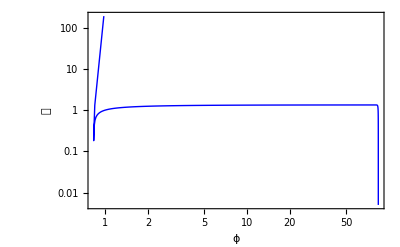

NDSolve::ndsz: At Ne == 63.3159, step size is effectively zero; singularity or stiff system suspected.

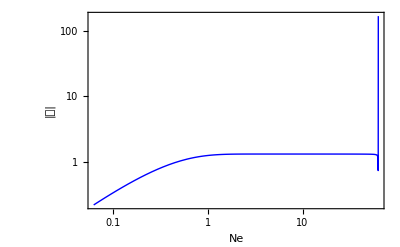

NDSolve::ndsz: At Ne == 63.3159, step size is effectively zero; singularity or stiff system suspected.

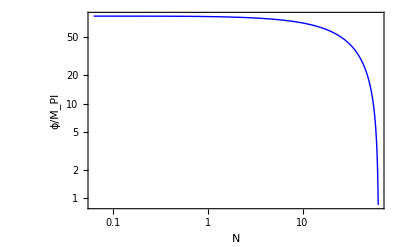

NDSolve::ndsz: At Ne == 63.3159, step size is effectively zero; singularity or stiff system suspected.

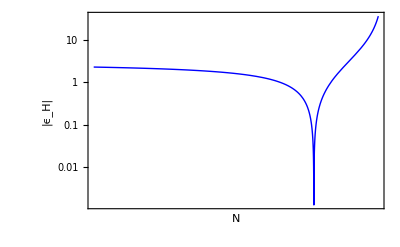

```mathematica
η=1
w=1
ϵ[Ne_,η_,w_]:=2-3 w-(2*(η+φ[Ne]))/φ[Ne]-(2*𝒰[Ne])/φ[Ne]

λ=1

κ=1

f2[En_]:=Sqrt[1+κ*En]

H[Ne_,η_,w_,En_]:=(ⅇ^(3 Ne w) f2[En]^(-3 w) √((φ[Ne])^2/λ))/(2 √6 √(η+φ[Ne]+𝒰[Ne]))

𝒰0=N[5*10^(-3)]

φ0=N[0.83*10^2]

sol[η_]:=NDSolve[{𝒰'[Ne]==-4 η-3 𝒰[Ne]-(4 η^2)/φ[Ne]-(6 η 𝒰[Ne])/φ[Ne]-(2 𝒰[Ne]^2)/φ[Ne],φ'[Ne]==𝒰[Ne],𝒰[0]==𝒰0,φ[0]==φ0},{𝒰,φ},{Ne,0,10^4}]

ϕ[Ne_]:=η+φ[Ne]

ParametricPlot[Evaluate[{ϕ[Ne],Abs[𝒰[Ne]]}/.sol[η]],{Ne,0,63.3159},AspectRatio->1/GoldenRatio,Frame->True,PlotRange->All,Axes->True,FrameLabel->{"ϕ","𝒰"},ScalingFunctions->{"Log","Log"},Epilog->{Red,PointSize[0.02],Point[Evaluate[{Abs[ϕ[0]],Abs[𝒰[0]]}/.sol[η]]],Blue,PointSize[0.02],Point[Evaluate[{Abs[ϕ[63.3159]],Abs[𝒰[63.3159]]}/.sol[η]]]},FrameStyle->Thick,LabelStyle->Directive[Black,Bold],PlotStyle->{Blue,Thick},AspectRatio->1/GoldenRatio]

Plot[Evaluate[{Abs[𝒰[Ne]]}/.sol[η]],{Ne,0,63.3159},Frame->True,PlotRange->All,Axes->True,FrameLabel->{"Ne","|𝒰|"},ScalingFunctions->{"Log","Log"},FrameStyle->Thick,LabelStyle->Directive[Black,Bold],PlotStyle->{Blue,Thick},AspectRatio->1/GoldenRatio]

Plot[Evaluate[{ϕ[Ne]}/.sol[η]],{Ne,0,63.3},Frame->True,PlotRange->All,Axes->True,ScalingFunctions->{"Log","Log"},FrameLabel->{"N","ϕ/M_Pl"},FrameStyle->Thick,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue,Thick},AspectRatio->1/GoldenRatio]

Plot[Evaluate[{Abs[ϵ[Ne,η,w]]}/.sol[η]],{Ne,62.5,63.3},Frame->True,PlotRange->All,Axes->True,FrameLabel->{"N","|ϵ_H|"},ScalingFunctions->{"Log","Log"},FrameStyle->Thick,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue,Thick},AspectRatio->1/GoldenRatio]
```